## Simulazioni

```mathematica
v2 = (x'[t] + l θ'[t]*Cos[θ[t]])^2 + ( l θ'[t]*Sin[θ[t]])^2;
T = 1/2 *M*x'[t]^2       + 1/2* m*v2    + 1/2*(J - m l^2)*θ'[t]^2 ;
V = m*g*l*Cos[θ[t]];
L = T - V;

e1 =D[D[L, x'[t]], t] - D[L, x[t]] == +u[t];
e2 = D[D[L, θ'[t]], t] - D[L, θ[t]] ==0 //Simplify;
motionEquations = Simplify[Solve[e1 && e2, {x''[t], θ''[t]}]][[1]];

params = {
	g ->9.8,
	l -> .113,
	m -> .022,
	M -> .210,
J->3.6*10^-4,
r11->1,
q11->1
};
```

```mathematica
Simplify[Solve[e1, { x''[t]}]][[1]] //TraditionalForm 
Simplify[Solve[e2, { θ''[t]}]][[1]] //TraditionalForm
motionEquations[[1, 2]]//Simplify//TraditionalForm
motionEquations[[2, 2]] //Simplify // TraditionalForm
```

{x''(t)→(-l m θ''(t) cos(θ(t))+l m (θ'(t))^2 sin(θ(t))+u(t))/(m+M)}

{θ''(t)→(l m (g sin(θ(t))-cos(θ(t)) x''(t)))/J}

(l m sin(θ(t)) (J (θ'(t))^2-g l m cos(θ(t)))+J u(t))/(J (m+M)-l^2 m^2 cos^2(θ(t)))

(l m (sin(θ(t)) (l m (θ'(t))^2 cos(θ(t))-g (m+M))+u(t) cos(θ(t))))/(l^2 m^2 cos^2(θ(t))-J (m+M))

```mathematica
ssm = StateSpaceModel[
	{e1, e2},
	{
    {x[t],0},
		{x'[t], 0},
		{θ[t], 0},
		{θ'[t], 0}
	},
	{u[t]},
	{θ[t], x[t], θ'[t]},
	t
]  //Simplify;
A = ssm[[1, 1]];
B = ssm[[1, 2]];

Q = ResourceFunction["HessianMatrix"][T-V, {x[t], x'[t],θ[t], θ'[t]}]  /. {x[t] -> 0, x'[t] ->0, θ[t] -> 0, θ'[t] -> 0};
Q +=  DiagonalMatrix[{q11, 0, 0, 0}];
R = DiagonalMatrix[{r11}];
```

```mathematica
A//MatrixForm
B//MatrixForm
{B, A.B, A.A.B, A.A.A.B} //MatrixForm
Q//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | (g l^2 m^2)/(l^2 m^2-J (m+M)) | 0
0 | 0 | 0 | 1
0 | 0 | -(g l m (m+M))/(l^2 m^2-J (m+M)) | 0)

(0
J/(-l^2 m^2+J (m+M))
0
(l m)/(l^2 m^2-J (m+M)))

((0) | (J/(-l^2 m^2+J (m+M))) | (0) | ((l m)/(l^2 m^2-J (m+M)))
(J/(-l^2 m^2+J (m+M))) | (0) | ((l m)/(l^2 m^2-J (m+M))) | (0)
(0) | ((g l^3 m^3)/((l^2 m^2-J (m+M))^2)) | (0) | (-(g l^2 m^2 (m+M))/((l^2 m^2-J (m+M))^2))
((g l^3 m^3)/((l^2 m^2-J (m+M))^2)) | (0) | (-(g l^2 m^2 (m+M))/((l^2 m^2-J (m+M))^2)) | (0))

(q11 | 0 | 0 | 0
0 | m+M | 0 | l m
0 | 0 | g l m | 0
0 | l m | 0 | J)

```mathematica
s[t_]:= {x[t],  x'[t], θ[t], θ'[t] };
simulateSystem[control_, T_, initialConditions_] := (
eqns = {
		e1, e2, s[0]==initialConditions
} /. params /. {u[t]->control};
solutions =  NDSolve[eqns, {x, θ}, {t, 0, T}];

{x[t], D[x[t], t], θ[t], D[θ[t], t]} /. solutions[[1]]
);

costIntegrand[s_, control_, trajectory_] :=  (Transpose[trajectory].Q.trajectory + Transpose[control].R.control )/. params  /. t->s
```

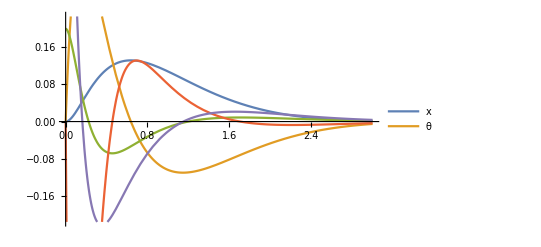

1.82129

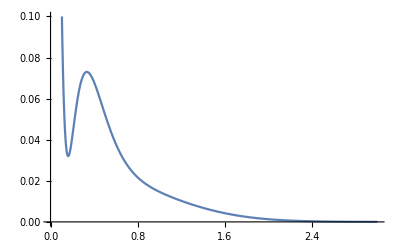

```mathematica
K = LQRegulatorGains[ssm /. params, {Q, R} /. params];

T = 3;
solutionsLQR = simulateSystem[-K.s[t], T, {0, 0, .2 ,0}];

Plot[{Evaluate[solutionsLQR], -K.solutionsLQR}, {t, 0, T},PlotLegends->{x, θ}]
costIntegrand[0, -K.solutionsLQR, solutionsLQR]

Plot[costIntegrand[t, -K.solutionsLQR, solutionsLQR], {t, 0, T}]
```